Типовой расчет. Вариант 6

Задание 2

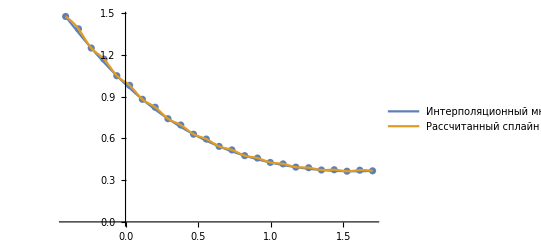

```mathematica
"Типовой расчет. Вариант 6"
"Задание 2"
(*Табличные данные*)
data= {{-0.412,1.47756},{-0.324,1.38862},{-0.236,1.25078},{-0.148, 1.17048},{-0.06,1.05118},{0.028,0.982116},{0.116,0.8818},{0.204,0.824781},{0.292,0.742362},{0.38,0.697},{0.468,0.630556},{0.556,0.595805},{0.644,0.543107},{0.732,0.517675},{0.82,0.476544},{0.908,0.459175},{0.996,0.427691},{1.084,0.417327},{1.172,0.393931},{1.26,0.389793},{1.348,0.373315},{1.436,0.374944},{1.524,0.3646},{1.612,0.371874},{1.7,0.367249}};
l=Length[data];

(*Встроенная функция для нахождения интерполяционного полинома*)
(*перенос данных в контейнеры xdata и ydata*)
For[i=0,i<l,i++,
xdata[i] = data[[i+1]][[1]];
ydata[i]=data[[i+1]][[2]];
];
(*Интерполяционный многочлен встроенной функции*)
inpln:=InterpolatingPolynomial[data,x];Collect[inpln,x];
gripln = Plot[inpln,{x,-0.5,1.788}];


(*Многочлен, полученнный в результате задания 1, при использовании значений функции в нечетных узлах (n=12)*)
data1= {{-0.412,1.47756},{-0.236,1.25078},{-0.06,1.05118},{0.116,0.8818},{0.292,0.742362},{0.468,0.630556},{0.644,0.543107},{0.82,0.476544},{0.996,0.427691},{1.172,0.393931},{1.348,0.373315},{1.524,0.3646}};
l1=Length[data1];

For[i=0,i<l1,i++,
xdata1[i] = data1[[i+1]][[1]];
ydata1[i]=data1[[i+1]][[2]];
];

n1=l1-1;
(*создание и заполнение таблицы разностей*)
Array[xdata1,{n1+1,0}];
Array[ydata1,{n1+1,0}];
pln1=∑_(i=0)^n1 ydata1[i]*∏_(j=0)^n1 If[i!=j,(x-xdata1[j])/(xdata1[i]-xdata1[j]),1];
(*формирование интерполяционного многочлена Лагранжа*)
lgr1[x_]:=Collect[pln1,x];

n = l-1;
Array[d,n,0];Array[w,n,0];Array[{p,q,r,o},n,1];
For[i=0,i<=n,i++,  (*Метод прогонки для расчета коэффициентов сплайна*)
d[i]=xdata[i+1]-xdata[i];
w[i]=ydata[i+1]-ydata[i]];
p[1]=0;r[n]=0;
For[i=1,i<=n,i++,
p[i]=d[i-1];
r[i]=d[i];
q[i]=2*(d[i]+d[i-1]);
o[i]=3*(w[i]/d[i]-w[i-1]/d[i-1])];
Array[u,n,1];Array[v,n,1];Array[cs,n,0];
u[1]=-r[1]/q[1];
v[1]=o[1]/q[1];
For[i=2,i<n,i++,
s=q[i]+p[i]*u[i-1];
u[i]=-r[i]/s;
v[i]=(o[i]-p[i]*v[i-1])/s];
cs[0]=0;
cs[n]=0;
For[i=n-1,i>=1,i--,
cs[i]=u[i]*cs[i+1]+v[i]];
spln[xdata_,ydata_,cs_,n_,x_]:=Block[{i=0,h1,a1,b1,c1,d1,t1},While[x>xdata[i+1],i++];(*Расчет коэффициентов рассчитанного сплайна*)
h1=xdata[i+1]-xdata[i];
a1=ydata[i];
b1=(ydata[i+1]-ydata[i])/h1-(cs[i+1]+2*cs[i])*h1/3;
c1=cs[i];
d1=(cs[i+1]-cs[i])/(3*h1);
t1=x-xdata[i];
Return[a1+b1*t1+c1*t1*t1+d1*t1*t1*t1]];
sq[x_]:=spln[xdata,ydata,cs,n,x](*функция-ссылка на рассчитанный сплайн spln*)
gr1:=ListPlot[data];
gr2:=Plot[{lgr1[x],sq[x]},{x,xdata[0],xdata[n]},PlotLegends->{"Интерполяционный многочлен Лангранжа 11-ой степени","Рассчитанный сплайн"}]
Show[{gr1,gr2}]
```